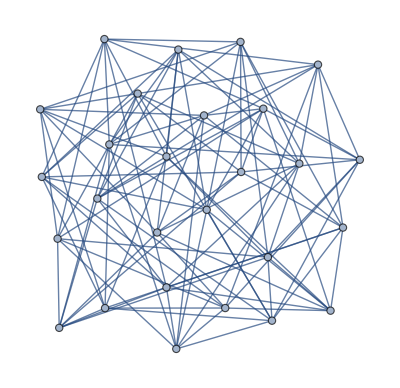

```mathematica
JR27=ImportString["Z{eCCECSQaHCQIPcGo`gELD?iGpSg@BPO`bACjO?Yd?ASAXBOBK?BRJ?AUYO", "Graph6"]
```

```mathematica
IsomorphicGraphQ[
JR27,CirculantGraph[27,{1,2,3,4,5,6,7,8}]]
```

False

```mathematica
Do[If[
IsomorphicGraphQ[
JR27,CirculantGraph[27,{i8,i7,i6,i5,i4,i3,i2,i1}]
]
,Print[i8," ",i7," ",i6," ",i5," ",i4," ",i3," ",i2," ",i1]
],{i8,1,6},{i7,i8+1,7},{i6,i7+1,8},{i5,i6+1,9},{i4,i5+1,10},{i3,i4+1,11},{i2,i3+1,12},{i1,i2+1,13}]
```

```mathematica
GraphData["VertexTransitive",27][[5;;6]]
```

{{GeneralizedQuadrangleMinusSpread,{{2,4},1}},{GeneralizedQuadrangleMinusSpread,{{2,4},2}}}

```mathematica
GraphData[#,{"EdgeCount","VertexCount"}]&/@GraphData["VertexTransitive",27]
```

{{243,27},{54,27},{0,27},{135,27},{108,27},{108,27},{81,27},{81,27},{54,27},{135,27},{216,27},{216,27},{54,27}}

```mathematica
Do[G=GraphData["VertexTransitive",27][[5;;6]][[i]];
Print[IsomorphicGraphQ[JR27,GraphData[G]]],{i,1,2}]
```

False

True

```mathematica
JRGD=GraphData["VertexTransitive",27][[6]]
```

{GeneralizedQuadrangleMinusSpread,{{2,4},2}}

```mathematica
GraphData[JRGD,"FractionalChromaticNumber"]
```

9/2

```mathematica
GraphData[JRGD,"AlternateStandardNames"]
```

{}

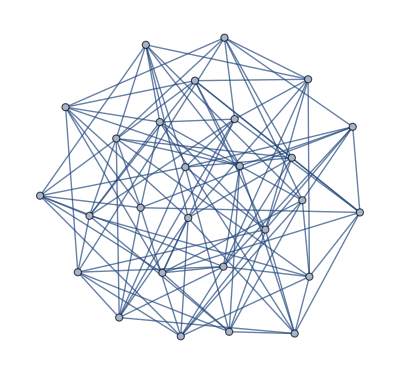

```mathematica
GraphPlot[GraphData[JRGD,"Edges","Rule"]]
```

```mathematica
GraphPlot[GraphData[JRGD,"AdjacencyMatrix"],VertexCoordinates->GraphData[JRGD,"VertexCoordinates"]]
```

GraphPlot[SparseArray[…],VertexCoordinates→Missing[NotAvailable]]